## A366478: a(n) = [(3*n^4 - 4*n^4 + n^2 + 4*n + 4) / 4.

### MATHEMATICA PROGRAM:

```mathematica
Table[(3n^4-4n^3+n^2+4n+4)/4,{n,0,38}] (* Paul F.Marrero Romero, Nov 02 2023 *)
```

{1,2,8,40,137,356,772,1478,2585,4222,6536,9692,13873,19280,26132,34666,45137,57818,73000,90992,112121,136732,165188,197870,235177,277526,325352,379108,439265,506312,580756,663122,753953,853810,963272,1082936,1213417,1355348,1509380}

### Formula:

G.f.: -(2*x^4+10*x^3+8*x^2-3*x+1)/(x-1)^5. -  Alois P. Heinz, Nov 02 2023

### Plot section:

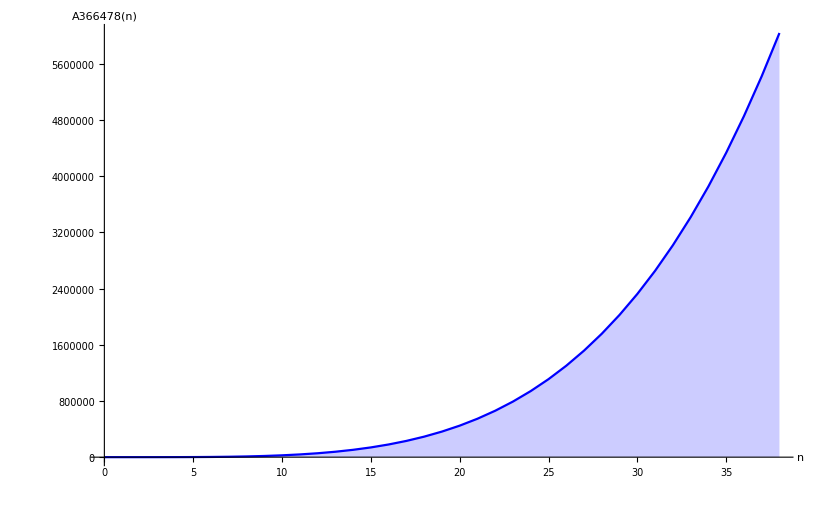

```mathematica
DiscretePlot[3n^4-4n^3+n^2+4n+4/4,{n,0,38}, Joined->True, PlotStyle-> Blue, AxesLabel->{"n","A366478(n)"}, LabelStyle->Directive[Black,Bold]]
```

### References:

N. J. A. Sloane, a(n) = (3*n^4 - 4*n^3 + n^2 + 4*n + 4)/4., Entry A366478 in The On-Line Encyclopedia of Integer Sequences, https://oeis.org/A366478